```mathematica
ClearAll;
```

```mathematica
a[u_,v_]:=Integrate[k D[u[x,y],{{x,y}}] D[v[x,y],{{x,y}}],{x,x1,x2},{y,y1,y2}]
```

```mathematica
b[v_]:=Integrate[v[x,y] f[x,y],{x,x1,x2},{y,y1,y2}]
```

```mathematica
n=10;
```

```mathematica
idx[n_]:=Module[{index},index=Table[0,n,n] ;
index[[1,All]]=-1;index[[All,1]]=-1;
index[[n,All]]=-1;index[[All,n]]=-1;
Do[Do[index[[i,j]]=(j-1)+(i-2) (n-2) ,{i,2,n-1}],{j,2,n-1}];
index]
```

```mathematica
idx[5]//MatrixForm
```

(-1 | -1 | -1 | -1 | -1
-1 | 1 | 2 | 3 | -1
-1 | 4 | 5 | 6 | -1
-1 | 7 | 8 | 9 | -1
-1 | -1 | -1 | -1 | -1)

```mathematica
basis[uh_]:=Module[{n,bas},
n=Sqrt[Dimensions[uh][[1]]] +2;
bas=Table[
If[idx[n][[i,j]] >0,
uh[[idx[n][[i,j]]]],
0]
,{i,1,n},{j,1,n}];
ListPlot3D[bas,DataRange->{{-1,1},{-1,1}},
Mesh->All,Ticks->None]]
```

```mathematica
uei[ne_,t_]:=
(* ne : Number of Element *)
(* t: Number of free nodes *)Table[If[j==i,1,0],{j,1,ne}]
```

```mathematica
Table[basis[uei[16,i]],{i,1,9}]//MatrixForm
```

(-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-)

#### 3. Set up a function to compute the element stiffness matrix Ke

```mathematica
detJ[x1_,x2_,x3_,y1_,y2_,y3_]:=(x1-x3)(y2-y3)-(x2-x3)(y1-y3);
```

```mathematica
Ke[x1_,x2_,x3_,y1_,y2_,y3_,k_]:=Module[{B,det},
det=detJ[x1,x2,x3,y1,y2,y3];
B=1/det{{y2-y3,y3-y1,y1-y2},{x3-x2,x1-x3,x2+x1}};
det/2 k Transpose[B].B]
```

Show that the element stiffness matrix is invariant w.r.t to a scaling of the node coordinates

```mathematica
Ke[x1,x2,x3,y1,y2,y3,k]==Ke[t x1,t x2,t x3,t y1,t y2,t y3,k]//Simplify
```

True

#### 4. Set up a function to compute the element load vector be

```mathematica
be[x1_,x2_,x3_,y1_,y2_,y3_,f_]:=detJ[x1,x2,x3,y1,y2,y3]/6 f {{1},{1},{1}}
```

Show that the element load vector depends quadratically on a scaling factor of the nod coordinates

```mathematica
t^2 be[x1,x2,x3,y1,y2,y3,f] == be[t x1, t x2, t x3, t y1, t y2 ,t y3,f]//FullSimplify
```

True

#### 5. Establish a function to compute the coefficients of the appromate solution u^hat

```mathematica
uhat[n_,kcoeff_,f_]:=Module[{d,nn,ke1,re1,k,r,n1,n2,n3,n4,nn1,nn2,ki1,ki2,kj1,kj2,ii,jj,i,j},
d=2/(n-1);
nn=(n-2)^2;

ke1=Ke[0,d,d,0,0,d,kcoeff];
re1=be[0,d,d,0,0,d,f];

k=Table[0,{i,1,nn},{j,1,nn}];
r=Table[0,{i,1,nn}];

For[i=1,i<n,i++,
For[j=1,j<n,j++,
n1=idx[n][[i,j]];
n2=idx[n][[i,j+1]];
n3=idx[n][[i+1,j]];
n4=idx[n][[i+1,j+1]];
nn1={n1,n2,n4};
nn2={n4,n3,n1};

For[ii=1,ii<=3,ii++,
ki1=nn1[[ii]];
ki2=nn2[[ii]];

If[ki1!=-1,r[[ki1]]+=re1[[ii]]];
If[ki2!=-1,r[[ki2]]+=re1[[ii]]];

For[jj=1,jj<=3,jj++,
kj1=nn1[[jj]];
kj2=nn2[[jj]];

If[ki1!=-1&&kj1!=-1,
k[[ki1,kj1]]+=ke1[[ii,jj]];];
If[ki2!=-1&&kj2!=-1,
k[[ki2,kj2]]+=ke1[[ii,jj]];];
];
];
];
];
Flatten[LinearSolve[N[k],N[r]]]
]
```

```mathematica
uhat[4,1,3]
```

{0.666667,0.666667,0.666667,0.666667}

#### 6. Study the convergence of the solution, compute a table of approximate solutions of n=5, 10,... ,50

```mathematica
uApp=Table[Max[uhat[i,1,3]],{i,5,50,5}]//N
```

{0.84375,0.857319,0.880526,0.877991,0.88285,0.881448,0.883454,0.882613,0.883697,0.883142}

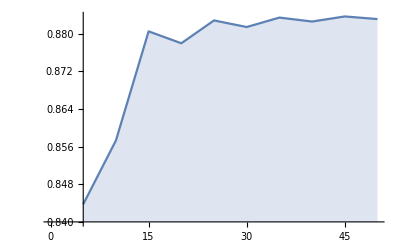

```mathematica
ListLinePlot[uApp,Filling->Axis,AxesOrigin->{5,0.84},DataRange->{5,50}]
```

Plot approximate solutions

```mathematica
GraphicsGrid[Partition[Table[basis[uhat[i,1,3]],{i,5,50,5}],3],ImageSize->Large]
```

-Graphics-